## Non-discrete calculation of E-field

### Here we turn the electric potential values for a 1x1 cube we have into electric field values

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis\ComputationalPhysicsFinalProj

For comparison, here is the discrete field we calculated

```mathematica
Ezero = {2/3,0,0}
EzeroTable = Table[Flatten[Ezero], length];
```

{2/3,0,0}

```mathematica
length10
length12
length14
length16
length18
```

306

442

650

898

1122

```mathematica
Rpotential[r_,j_, newSides_]:=1/(Norm[r- newSides[[j]]])
```

```mathematica
SetDirectory["C:\\Users\\Lara\\Documents\\Physics\\Witten\\Electrophoreses\\Electrophoresis\\"]
<<smallDenseCubeFieldFinal.mx
newSides20 = newSides;
density20 = density;
normal20 = normal;
length20= length;
EMatrix20 = EMatrix;
R20= R;
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis

```mathematica
normalOfField20=Table[EzeroTable[[i]].normal20[newSides20[[i]]], {i, length20}];
Q20= LinearSolve[EMatrix20, normalOfField20];
EField20[r_] := Sum[If[r ==newSides20[[j]], 2Pi/density20[j]*normal20[newSides20[[j]]]*Q20[[j]], R20[r, j]*Q20[[j]]], {j,length20}]+Ezero
Potential20[r_] := Sum[If[r ==newSides20[[j]], 2Pi*(Sqrt[density20[j]/Pi])/density20[j]*Q20[[j]], Rpotential[r, j, newSides20]*Q20[[j]]], {j,length20}]+ 2/3*r[[1]]
```

```mathematica
Length[newSides20]
```

1542

```mathematica
SetDirectory["C:\\Users\\Lara\\Documents\\Physics\\Witten\\Electrophoreses\\Electrophoresis\\ComputationalPhysicsFinalProj\\"]
<<smallDenseCubeFieldS10.mx
newSides10 = newSides;
density10 = density;
normal10 = normal;
length10= length;
EMatrix10 = EMatrix;
R10= R;
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis\ComputationalPhysicsFinalProj

```mathematica
normalOfField10=Table[EzeroTable[[i]].normal10[newSides10[[i]]], {i, length10}];
Q10= LinearSolve[EMatrix10, normalOfField10];
EField10[r_] := Sum[If[r ==newSides10[[j]], 2Pi/density10[j]*normal10[newSides10[[j]]]*Q10[[j]], R10[r, j]*Q10[[j]]], {j,length10}]+Ezero
Potential10[r_] := Sum[If[r ==newSides10[[j]], 2Pi*(Sqrt[density10[j]/Pi])/density10[j]*Q10[[j]], Rpotential[r, j, newSides10]*Q10[[j]]], {j,length10}]+ 2/3*r[[1]]
```

```mathematica
<<smallDenseCubeFieldS12.mx
newSides12 = newSides;
density12 = density;
normal12= normal;
length12= length;
EMatrix12 = EMatrix;
R12= R;
```

```mathematica
normalOfField12=Table[EzeroTable[[i]].normal12[newSides12[[i]]], {i, length12}];
Q12= LinearSolve[EMatrix12, normalOfField12];
EField12[r_] := Sum[If[r ==newSides12[[j]], 2Pi/density12[j]*normal12[newSides12[[j]]]*Q12[[j]], R12[r, j]*Q12[[j]]], {j,length12}]+Ezero
Potential12[r_] := Sum[If[r ==newSides12[[j]], 2Pi*(Sqrt[density12[j]/Pi])/density12[j]*Q12[[j]], Rpotential[r, j, newSides12]*Q12[[j]]], {j,length12}]+ 2/3*r[[1]]
```

```mathematica
<<smallDenseCubeFieldS14.mx
newSides14 = newSides;
density14= density;
normal14 = normal;
length14= length;
EMatrix14 = EMatrix;
R14= R;
```

```mathematica
normalOfField14=Table[EzeroTable[[i]].normal14[newSides14[[i]]], {i, length14}];
Q14= LinearSolve[EMatrix14, normalOfField14];
EField14[r_] := Sum[If[r ==newSides14[[j]], 2Pi/density14[j]*normal14[newSides14[[j]]]*Q14[[j]], R14[r, j]*Q14[[j]]], {j,length14}]+Ezero
Potential14[r_] := Sum[If[r ==newSides14[[j]], 2Pi*(Sqrt[density14[j]/Pi])/density14[j]*Q14[[j]], Rpotential[r, j, newSides14]*Q14[[j]]], {j,length14}]+ 2/3*r[[1]]
```

```mathematica
<<smallDenseCubeFieldS16.mx
newSides16 = newSides;
density16= density;
normal16 = normal;
length16= length;
EMatrix16 = EMatrix;
R16= R;
```

```mathematica
normalOfField16=Table[EzeroTable[[i]].normal16[newSides16[[i]]], {i, length16}];
Q16= LinearSolve[EMatrix16, normalOfField16];
EField16[r_] := Sum[If[r ==newSides16[[j]], 2Pi/density16[j]*normal16[newSides16[[j]]]*Q16[[j]], R16[r, j]*Q16[[j]]], {j,length16}]+Ezero
Potential16[r_] := Sum[If[r ==newSides16[[j]], 2Pi*(Sqrt[density16[j]/Pi])/density16[j]*Q16[[j]], Rpotential[r, j, newSides16]*Q16[[j]]], {j,length16}]+ 2/3*r[[1]]
```

```mathematica
<<smallDenseCubeFieldS18.mx
newSides18 = newSides;
density18= density;
normal18 = normal;
length18= length;
EMatrix18 = EMatrix;
R18= R;
```

```mathematica
normalOfField18=Table[EzeroTable[[i]].normal18[newSides18[[i]]], {i, length18}];
Q18= LinearSolve[EMatrix18, normalOfField18];
EField18[r_] := Sum[If[r ==newSides18[[j]], 2Pi/density18[j]*normal18[newSides18[[j]]]*Q18[[j]], R18[r, j]*Q18[[j]]], {j,length18}]+Ezero
Potential18[r_] := Sum[If[r ==newSides18[[j]], 2Pi*(Sqrt[density18[j]/Pi])/density18[j]*Q18[[j]], Rpotential[r, j, newSides18]*Q18[[j]]], {j,length18}]+ 2/3*r[[1]]
```

```mathematica
length18
```

1122

{2/3,0,0}

```mathematica
Dimensions[EMatrix]
Length[newSides]
```

{1542,1542}

1542

```mathematica
Length[newSides]
```

650

The discrete potential:

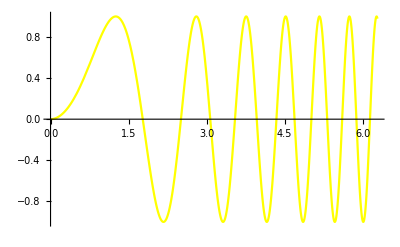

```mathematica
Plot[Sin[x^2],{x,0,2Pi},PlotStyle->RGBColor[1,1,0]]
```

Because the box we used discrete data on did not have the same dimensions as the one from the non-discrete data, we have to make sure to account for the difference in dimensions when we compare the data by multiplying the results by the half side length of one of the data sets divided by the half sidelength of the other

```mathematica
BoundingRegion[boxCentered]
```

Cuboid[{-0.4,-0.43301,-0.433015},{0.4,0.43301,0.433015}]

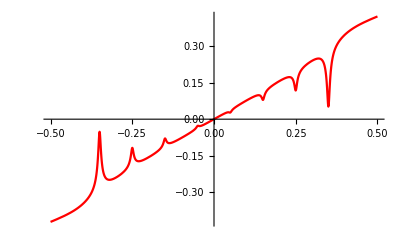

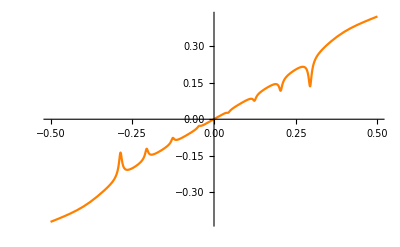

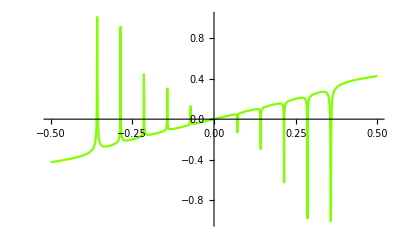

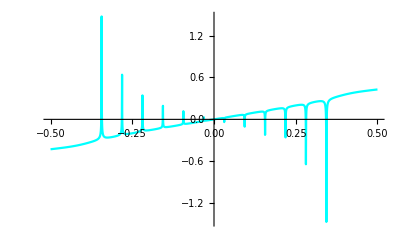

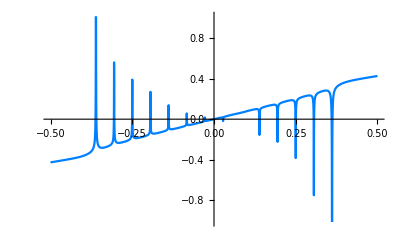

```mathematica
Plot[Potential10[{x, BoundingRegion[newSides10][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[1,0,0]]
Plot[Potential12[{x, BoundingRegion[newSides12][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[1,0.5,0]]
Plot[Potential14[{x, BoundingRegion[newSides14][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[.5,1,0]]
Plot[Potential16[{x, BoundingRegion[newSides16][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[0,1,1]]
Plot[Potential18[{x, BoundingRegion[newSides18][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[0,.5,1]]
```

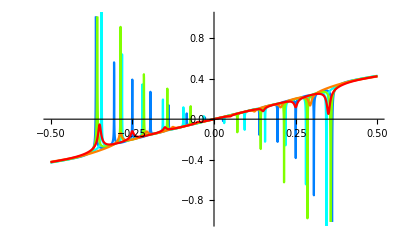

```mathematica
Show[%,%%,%%%,%%%%,%%%%%]
```

```mathematica
BoundingRegion[newSides10][[-1]][[1]]
```

0.4

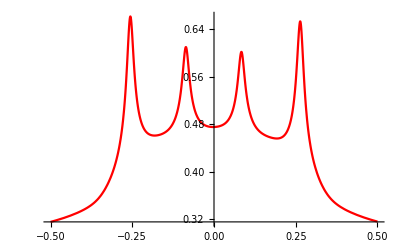

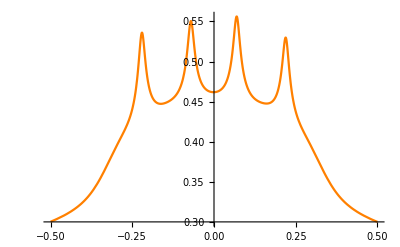

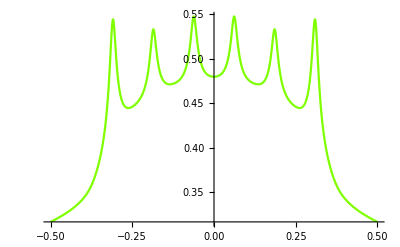

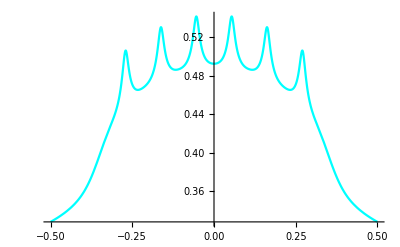

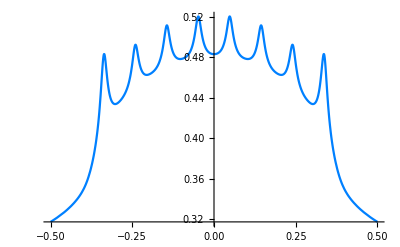

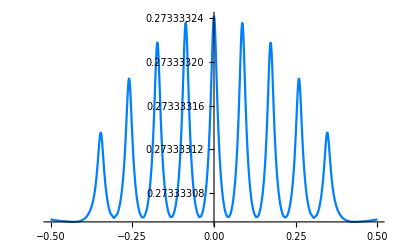

```mathematica
Plot[Potential10[{BoundingRegion[newSides10][[-1]][[1]]+.01,x,0}], {x, -.5,.5}, PlotStyle->RGBColor[1,0,0]]
Plot[Potential12[{BoundingRegion[newSides12][[-1]][[1]]+.01,x,0}], {x, -.5,.5}, PlotStyle->RGBColor[1,0.5,0]]
Plot[Potential14[{BoundingRegion[newSides14][[-1]][[1]]+.01,x,0}], {x, -.5,.5}, PlotStyle->RGBColor[.5,1,0]]
Plot[Potential16[{BoundingRegion[newSides16][[-1]][[1]]+.01,x,0}], {x, -.5,.5}, PlotStyle->RGBColor[0,1,1]]
Plot[Potential18[{BoundingRegion[newSides18][[-1]][[1]]+.01,x,0}], {x, -.5,.5}, PlotStyle->RGBColor[0,.5,1]]
Plot[Potential20[{BoundingRegion[newSides20][[-1]][[1]]+.01,x,0}], {x, -.5,.5}, PlotStyle->RGBColor[0,.5,1]]
```

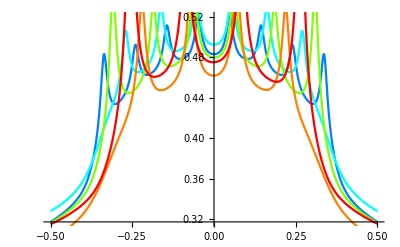

```mathematica
Show[%,%%,%%%,%%%%,%%%%%]
```

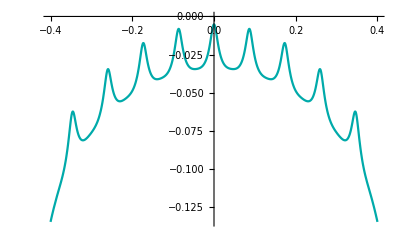

```mathematica
Plot[Potential[{BoundingRegion[boxCentered][[1]][[1]],x,0.01}], {x, -.4,.4}, PlotStyle->Darker[Cyan]]
```

```mathematica
sidedata = Import["cube_potential_side.txt", "Table"];
```

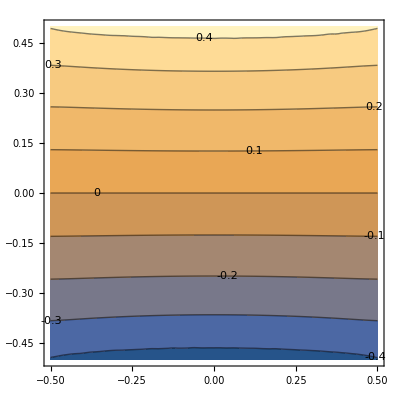

```mathematica
ListContourPlot[sidedata, ContourLabels->All]
```

```mathematica
topdata = Import["cube_potential_top.txt", "Table"];
```

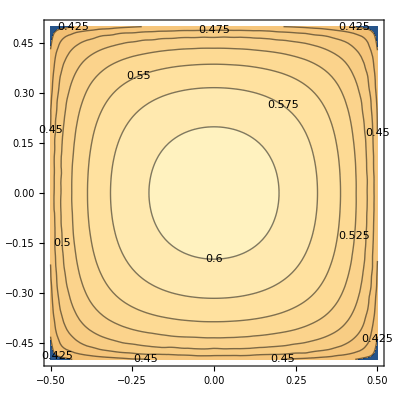

```mathematica
ListContourPlot[topdata, ContourLabels->All]
```

## Construct E fields

### We interpolated the potential at each point form the known data points:

```mathematica
topdata[[1]]
```

{-0.5,-0.5,0.405716000000000021}

```mathematica
sideFunction=Interpolation[{{#[[1]], #[[2]]},#[[3]]}&/@sidedata]
```

InterpolatingFunction[…]

```mathematica
sideFunction
```

```mathematica
topfunction=Interpolation[{{#[[1]], #[[2]]},#[[3]]}&/@topdata]
```

InterpolatingFunction[…]

```mathematica
BoundingRegion[newSides10]
BoundingRegion[newSides12]
BoundingRegion[newSides14]
BoundingRegion[newSides16]
BoundingRegion[newSides18]
```

Cuboid[{-0.4,-0.346054,-0.435973},{0.4,0.343946,0.434027}]

Cuboid[{-0.376062,-0.360579,-0.435811},{0.373938,0.359421,0.434189}]

Cuboid[{-0.392861,-0.371154,-0.433194},{0.392859,0.371156,0.433806}]

Cuboid[{-0.40625,-0.378886,-0.433196},{0.40625,0.378884,0.433804}]

Cuboid[{-0.388888,-0.384901,-0.433195},{0.388892,0.384899,0.433805}]

```mathematica
Plot[sideFunction[.01*.5/0.43597297297297294, z*.5/0.43597297297297294], {z, -.43301,.43301}, PlotStyle->Darker[Cyan]]
```

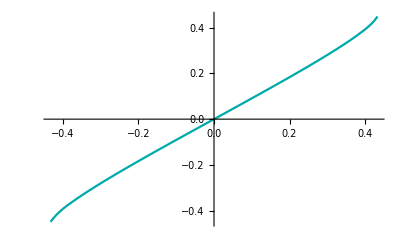

```mathematica
Show[%208,PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

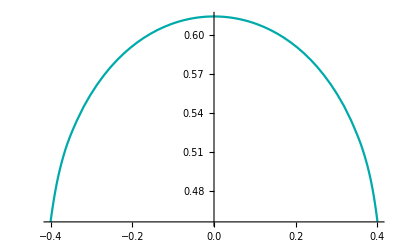

```mathematica
Plot[topfunction[x*.5/0.4, 0.01*.5/0.4], {x, -.4,.4}, PlotStyle->Darker[Cyan]]
```

```mathematica
BoundingRegion[newSides10][[1]][[3]]
```

-0.435973

```mathematica
BoundingRegion[newSides10][[1]][[3]]
```

-0.435973

Comparing the potentials

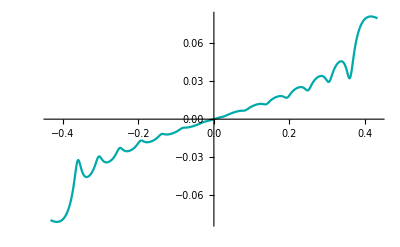

```mathematica
Plot[{Potential18[{x,BoundingRegion[newSides18][[-1]][[2]],.01}]-sideFunction[.01*2*BoundingRegion[newSides18][[-1]][[2]], x*2*BoundingRegion[newSides18][[-1]][[3]]]},{x, BoundingRegion[newSides18][[1]][[3]],BoundingRegion[newSides18][[-1]][[3]]}, PlotStyle->Darker[Cyan]]
```

S12

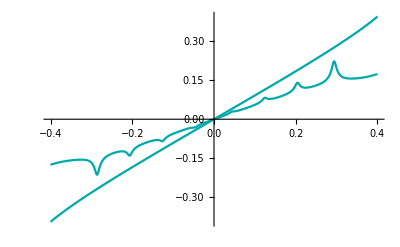

S10

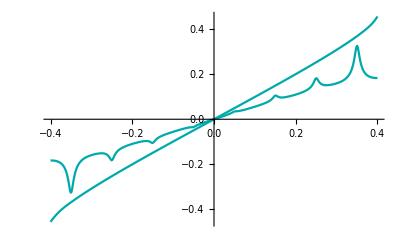

```mathematica
BoundingRegion[newSides20][[-1]][[2]]
```

0.43301

```mathematica
Potential20[{.4,BoundingRegion[newSides20][[-1]][[2]],.01}]
```

0.265398

```mathematica
sideFunction[.01*2*BoundingRegion[newSides20][[-1]][[2]], .4*2*BoundingRegion[newSides20][[-1]][[3]]]
```

0.2825

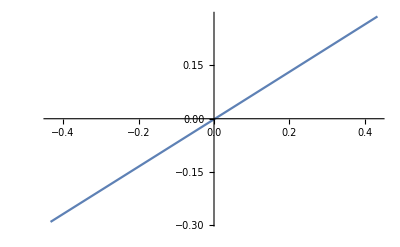

```mathematica
Plot[Potential20[{x,BoundingRegion[newSides20][[-1]][[2]],.01}],{x, BoundingRegion[newSides20][[1]][[3]],BoundingRegion[newSides20][[-1]][[3]]}]
```

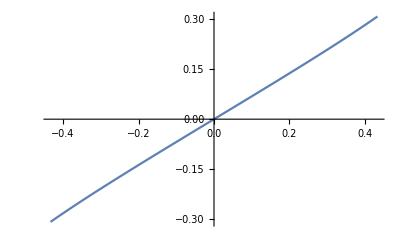

```mathematica
Plot[{sideFunction[.01*2*BoundingRegion[newSides20][[-1]][[2]], x*2*BoundingRegion[newSides20][[-1]][[3]]]},{x, BoundingRegion[newSides20][[1]][[3]],BoundingRegion[newSides20][[-1]][[3]]}]
```

```mathematica
Plot[Potential10[{x, BoundingRegion[newSides10][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[1,0,0]]
Plot[Potential12[{x, BoundingRegion[newSides12][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[1,0.5,0]]
Plot[Potential14[{x, BoundingRegion[newSides14][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[.5,1,0]]
Plot[Potential16[{x, BoundingRegion[newSides16][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[0,1,1]]
Plot[Potential18[{x, BoundingRegion[newSides18][[1]][[2]],0}], {x, -.5,.5}, PlotStyle->RGBColor[0,.5,1]]
```

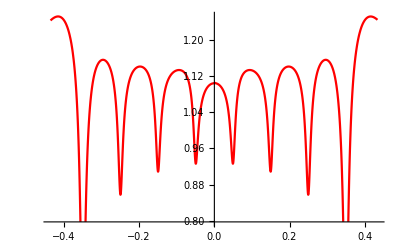

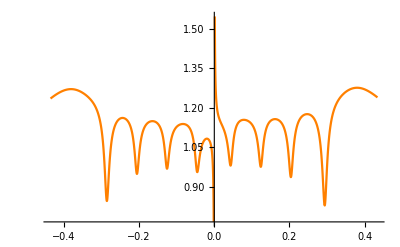

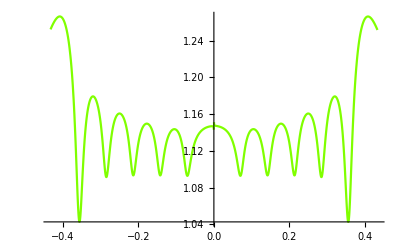

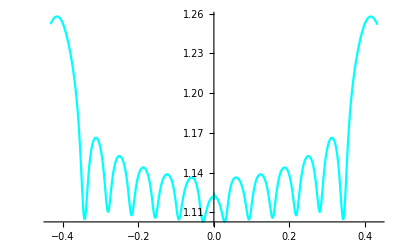

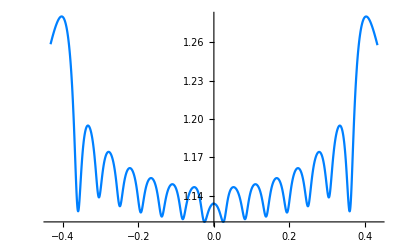

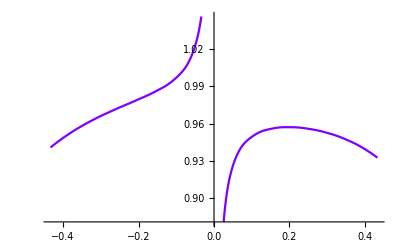

```mathematica
Plot[{Potential10[{x,BoundingRegion[newSides10][[-1]][[2]],.01}]/sideFunction[.01*2*BoundingRegion[newSides10][[-1]][[2]], x*2*BoundingRegion[newSides10][[-1]][[3]]]},{x, BoundingRegion[newSides10][[1]][[3]],BoundingRegion[newSides10][[-1]][[3]]}, PlotStyle->RGBColor[1,0,0]]
Plot[{Potential12[{x,BoundingRegion[newSides12][[-1]][[2]],.01}]/sideFunction[.01*2*BoundingRegion[newSides12][[-1]][[2]], x*2*BoundingRegion[newSides12][[-1]][[3]]]},{x, BoundingRegion[newSides12][[1]][[3]],BoundingRegion[newSides12][[-1]][[3]]}, PlotStyle->RGBColor[1,0.5,0]]
Plot[{Potential14[{x,BoundingRegion[newSides14][[-1]][[2]],.01}]/sideFunction[.01*2*BoundingRegion[newSides14][[-1]][[2]], x*2*BoundingRegion[newSides14][[-1]][[3]]]},{x, BoundingRegion[newSides14][[1]][[3]],BoundingRegion[newSides14][[-1]][[3]]}, PlotStyle->RGBColor[.5,1,0]]
Plot[{Potential16[{x,BoundingRegion[newSides16][[-1]][[2]],.01}]/sideFunction[.01*2*BoundingRegion[newSides16][[-1]][[2]], x*2*BoundingRegion[newSides16][[-1]][[3]]]},{x, BoundingRegion[newSides16][[1]][[3]],BoundingRegion[newSides16][[-1]][[3]]},   PlotStyle->RGBColor[0,1,1]]
Plot[{Potential18[{x,BoundingRegion[newSides18][[-1]][[2]],.01}]/sideFunction[.01*2*BoundingRegion[newSides18][[-1]][[2]], x*2*BoundingRegion[newSides18][[-1]][[3]]]},{x, BoundingRegion[newSides18][[1]][[3]],BoundingRegion[newSides18][[-1]][[3]]}, PlotStyle->RGBColor[0,.5,1]]
Plot[{Potential20[{x,BoundingRegion[newSides20][[-1]][[2]],.01}]/sideFunction[.01*2*BoundingRegion[newSides20][[-1]][[2]], x*2*BoundingRegion[newSides20][[-1]][[3]]]},{x, BoundingRegion[newSides20][[1]][[3]],BoundingRegion[newSides20][[-1]][[3]]}, PlotStyle->RGBColor[.5,0,1]]
```

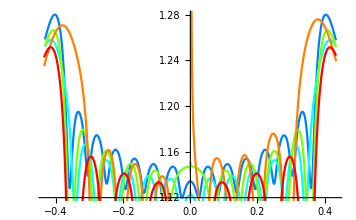

```mathematica
Show[%337, %336, %335, %334, %333]
```

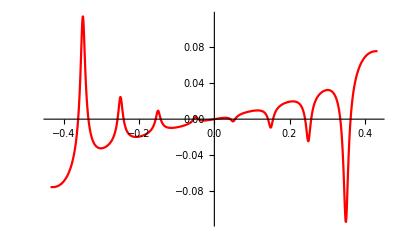

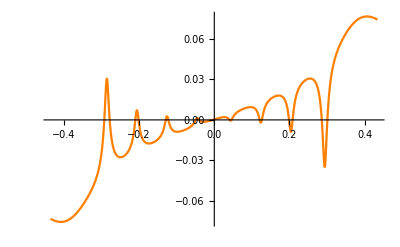

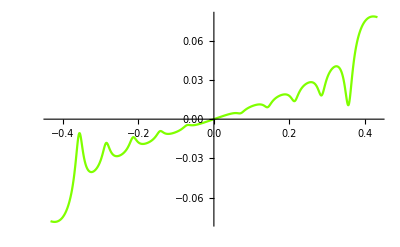

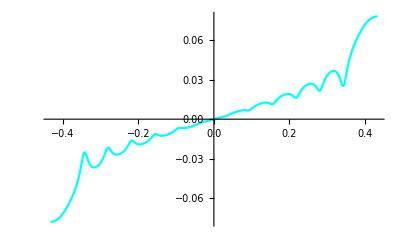

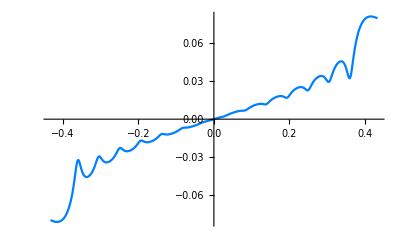

```mathematica
Plot[{Potential10[{x,BoundingRegion[newSides10][[-1]][[2]],.01}]-sideFunction[.01*2*BoundingRegion[newSides10][[-1]][[2]], x*2*BoundingRegion[newSides10][[-1]][[3]]]},{x, BoundingRegion[newSides10][[1]][[3]],BoundingRegion[newSides10][[-1]][[3]]}, PlotStyle->RGBColor[1,0,0]]
Plot[{Potential12[{x,BoundingRegion[newSides12][[-1]][[2]],.01}]-sideFunction[.01*2*BoundingRegion[newSides12][[-1]][[2]], x*2*BoundingRegion[newSides12][[-1]][[3]]]},{x, BoundingRegion[newSides12][[1]][[3]],BoundingRegion[newSides12][[-1]][[3]]}, PlotStyle->RGBColor[1,0.5,0]]
Plot[{Potential14[{x,BoundingRegion[newSides14][[-1]][[2]],.01}]-sideFunction[.01*2*BoundingRegion[newSides14][[-1]][[2]], x*2*BoundingRegion[newSides14][[-1]][[3]]]},{x, BoundingRegion[newSides14][[1]][[3]],BoundingRegion[newSides14][[-1]][[3]]}, PlotStyle->RGBColor[.5,1,0]]
Plot[{Potential16[{x,BoundingRegion[newSides16][[-1]][[2]],.01}]-sideFunction[.01*2*BoundingRegion[newSides16][[-1]][[2]], x*2*BoundingRegion[newSides16][[-1]][[3]]]},{x, BoundingRegion[newSides16][[1]][[3]],BoundingRegion[newSides16][[-1]][[3]]},   PlotStyle->RGBColor[0,1,1]]
Plot[{Potential18[{x,BoundingRegion[newSides18][[-1]][[2]],.01}]-sideFunction[.01*2*BoundingRegion[newSides18][[-1]][[2]], x*2*BoundingRegion[newSides18][[-1]][[3]]]},{x, BoundingRegion[newSides18][[1]][[3]],BoundingRegion[newSides18][[-1]][[3]]}, PlotStyle->RGBColor[0,.5,1]]
```

```mathematica
Show[%,%%,%%%,%%%%,%%%%%]
```

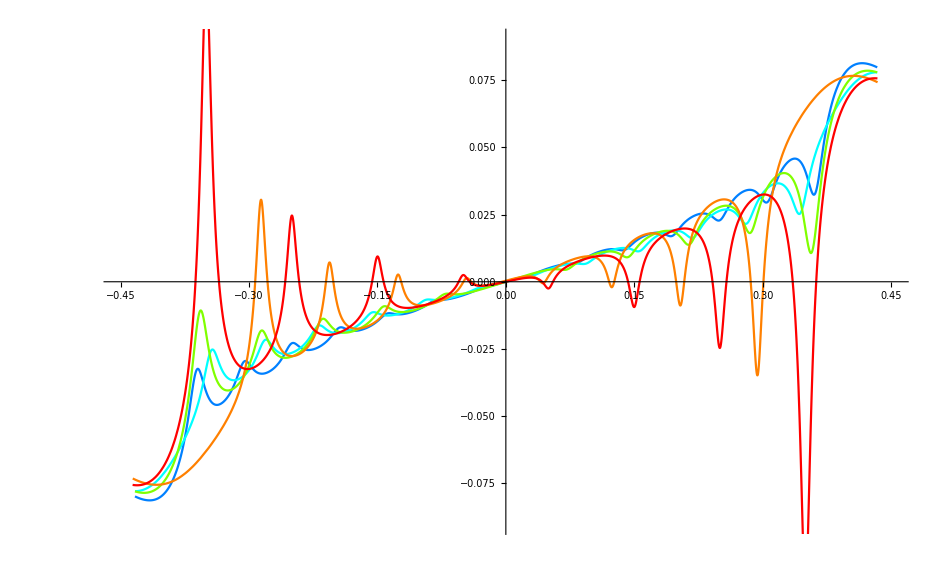

-Graphics-

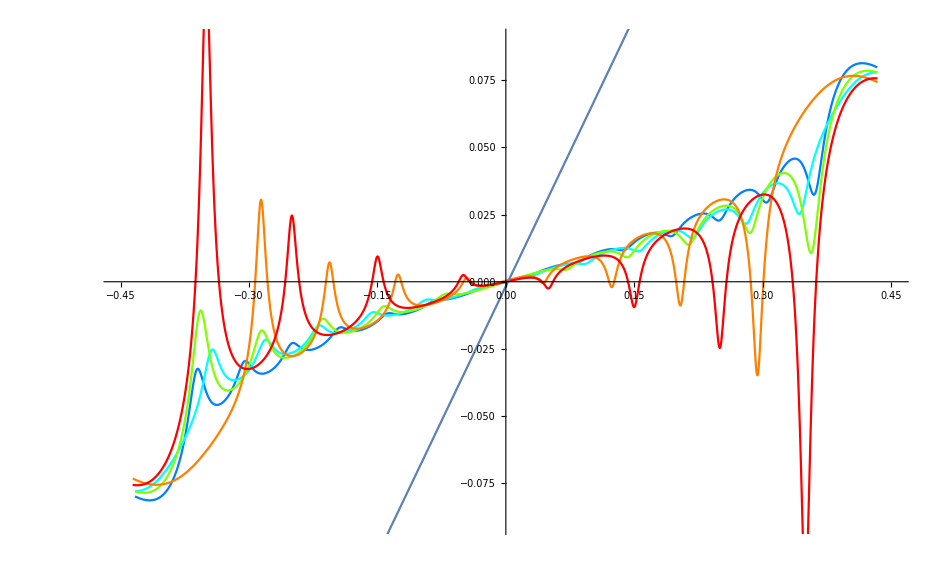

```mathematica
Show[%414, %361]
```

```mathematica
FindMinimum[Plot[{Potential10[{BoundingRegion[newSides10][[-1]][[1]],x,0.01}]/topfunction[x*.5/BoundingRegion[newSides10][[2]][[1]], 0.01*.5/BoundingRegion[newSides10][[2]][[1]]]}, {x, -BoundingRegion[newSides10][[2]][[1]],BoundingRegion[newSides10][[2]][[1]]},  PlotStyle->RGBColor[1,0,0]], {x, -BoundingRegion[newSides10][[2]][[1]]}]
```

FindMinimum::nrnum: The function value  is not a real number at {x} = {-0.4}.

FindMinimum[Plot[{Potential10[{BoundingRegion[newSides10]⟦-1⟧⟦1⟧,x,0.01}]/topfunction[(x 0.5)/(BoundingRegion[newSides10]⟦2⟧⟦1⟧),(0.01 0.5)/(BoundingRegion[newSides10]⟦2⟧⟦1⟧)]},{x,-BoundingRegion[newSides10]⟦2⟧⟦1⟧,BoundingRegion[newSides10]⟦2⟧⟦1⟧},PlotStyle→RGBColor[1, 0, 0]],{x,-BoundingRegion[newSides10]⟦2⟧⟦1⟧}]

```mathematica
Plot[{Potential10[{BoundingRegion[newSides10][[-1]][[1]],x,0.01}]/topfunction[x*.5/BoundingRegion[newSides10][[2]][[1]], 0.01*.5/BoundingRegion[newSides10][[2]][[1]]]}, {x, -BoundingRegion[newSides10][[2]][[1]],BoundingRegion[newSides10][[2]][[1]]},  PlotStyle->RGBColor[1,0,0]]
Plot[{Potential12[{BoundingRegion[newSides12][[-1]][[1]],x,0.01}]/topfunction[x*.5/BoundingRegion[newSides12][[2]][[1]], 0.01*.5/BoundingRegion[newSides12][[2]][[1]]]}, {x, -BoundingRegion[newSides12][[2]][[1]],BoundingRegion[newSides12][[2]][[1]]},  PlotStyle->RGBColor[1,0.5,0]]
Plot[{Potential14[{BoundingRegion[newSides14][[-1]][[1]],x,0.01}]/topfunction[x*.5/BoundingRegion[newSides14][[2]][[1]], 0.01*.5/BoundingRegion[newSides14][[2]][[1]]]}, {x, -BoundingRegion[newSides14][[2]][[1]],BoundingRegion[newSides14][[2]][[1]]},  PlotStyle->RGBColor[.5,1,0]]
Plot[{Potential16[{BoundingRegion[newSides16][[-1]][[1]],x,0.01}]/topfunction[x*.5/BoundingRegion[newSides16][[2]][[1]], 0.01*.5/BoundingRegion[newSides16][[2]][[1]]]}, {x, -BoundingRegion[newSides16][[2]][[1]],BoundingRegion[newSides16][[2]][[1]]},  PlotStyle->RGBColor[0,1,1]]
Plot[{Potential18[{BoundingRegion[newSides18][[-1]][[1]],x,0.01}]/topfunction[x*.5/BoundingRegion[newSides18][[2]][[1]], 0.01*.5/BoundingRegion[newSides18][[2]][[1]]]}, {x, -BoundingRegion[newSides18][[2]][[1]],BoundingRegion[newSides18][[2]][[1]]},  PlotStyle->RGBColor[0,.5,1]]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Show[%395,%394,%393,%392,%396]
```

-Graphics-

```mathematica
Show[%398,AxesStyle->Black]
```

-Graphics-

```mathematica
Show[%399,ImageSize->Large]
```

-Graphics-

```mathematica
Show[%400,AxesLabel->{HoldForm[Distance from left to right side of cube],None},PlotLabel->HoldForm[Ratio of expected top surface potential with discrete aproximation],LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[%401,PlotLabel->HoldForm[Ratio of expected top surface potential to discrete approximation]]
```

-Graphics-

```mathematica
Lines = {{306,.761}, {442,.74}, { 650,.77},{898,.79} , { 1122,.777}}
```

{{306,0.761},{442,0.74},{650,0.77},{898,0.79},{1122,0.777}}

```mathematica
LinearModelFit[Lines,x,x]
```

FittedModel[0.739645+0.0000408938 x]

```mathematica
1-0.7396450252951101
```

```mathematica
0.2603549747048899/0.00004089376053962843
```

6366.62

```mathematica
%461["AdjustedRSquared"]
```

0.367227

```mathematica
%430["BestFitParameters"]
```

{0.743,0.0082}

```mathematica
%430["ANOVATableMeanSquares"]
```

{0.0006724,0.000242933}

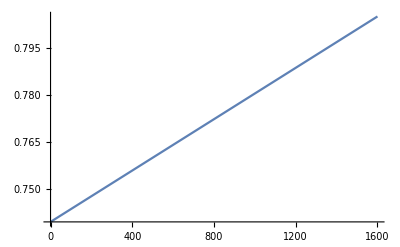

```mathematica
Plot[0.7396450252951101+0.00004089376053962843x , {x,0, 1600}]
```

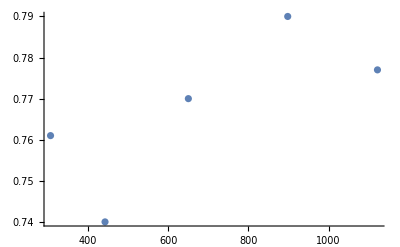

```mathematica
ListPlot[Lines,PlotRange-> Automatic]
```

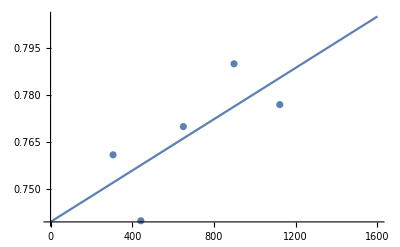

```mathematica
Show[%479,%480, PlotRange-> All]
```

```mathematica
Show[%488,Ticks->{Automatic,Automatic},AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[2.]],Method->{"AxesInFront"->False,"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

-Graphics-

```mathematica
Show[%490,PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

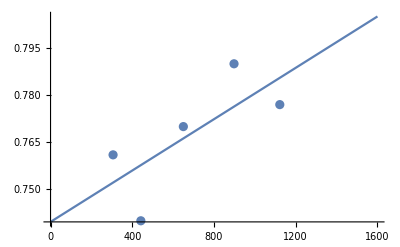

```mathematica
StandardDeviation[Lines]
```

0.0187163

```mathematica
Chi = (#-RootMeanSquare[Lines])^2 & /@ Lines
```

{0.000493616,0.0000849619,4.91721×10^-6,0.0000460026,0.000771868}

```mathematica
Total[Chi]
```

0.00140137

```mathematica
ChiSquareDistribution
```

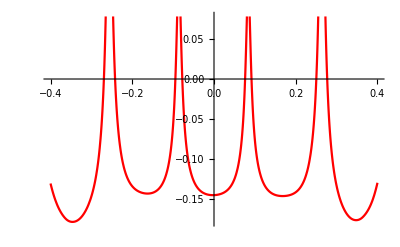

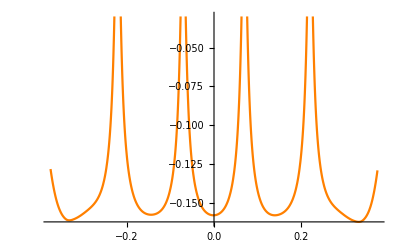

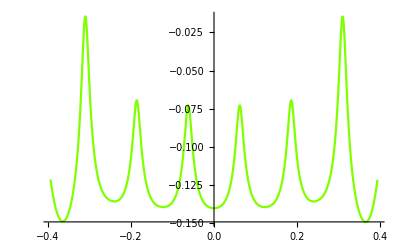

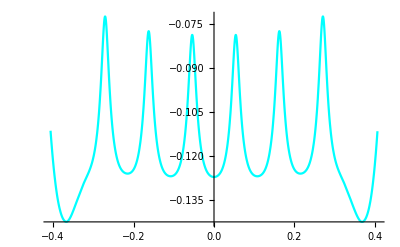

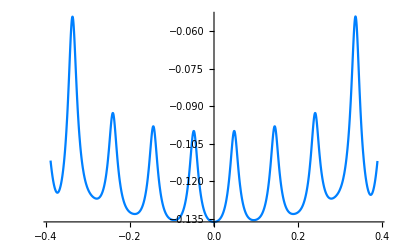

```mathematica
Plot[{Potential10[{BoundingRegion[newSides10][[-1]][[1]],x,0.01}]-topfunction[x*.5/BoundingRegion[newSides10][[2]][[1]], 0.01*.5/BoundingRegion[newSides10][[2]][[1]]]}, {x, -BoundingRegion[newSides10][[2]][[1]],BoundingRegion[newSides10][[2]][[1]]},  PlotStyle->RGBColor[1,0,0]]
Plot[{Potential12[{BoundingRegion[newSides12][[-1]][[1]],x,0.01}]-topfunction[x*.5/BoundingRegion[newSides12][[2]][[1]], 0.01*.5/BoundingRegion[newSides12][[2]][[1]]]}, {x, -BoundingRegion[newSides12][[2]][[1]],BoundingRegion[newSides12][[2]][[1]]},  PlotStyle->RGBColor[1,0.5,0]]
Plot[{Potential14[{BoundingRegion[newSides14][[-1]][[1]],x,0.01}]-topfunction[x*.5/BoundingRegion[newSides14][[2]][[1]], 0.01*.5/BoundingRegion[newSides14][[2]][[1]]]}, {x, -BoundingRegion[newSides14][[2]][[1]],BoundingRegion[newSides14][[2]][[1]]},  PlotStyle->RGBColor[.5,1,0]]
Plot[{Potential16[{BoundingRegion[newSides16][[-1]][[1]],x,0.01}]-topfunction[x*.5/BoundingRegion[newSides16][[2]][[1]], 0.01*.5/BoundingRegion[newSides16][[2]][[1]]]}, {x, -BoundingRegion[newSides16][[2]][[1]],BoundingRegion[newSides16][[2]][[1]]},  PlotStyle->RGBColor[0,1,1]]
Plot[{Potential18[{BoundingRegion[newSides18][[-1]][[1]],x,0.01}]-topfunction[x*.5/BoundingRegion[newSides18][[2]][[1]], 0.01*.5/BoundingRegion[newSides18][[2]][[1]]]}, {x, -BoundingRegion[newSides18][[2]][[1]],BoundingRegion[newSides18][[2]][[1]]},  PlotStyle->RGBColor[0,.5,1]]
```

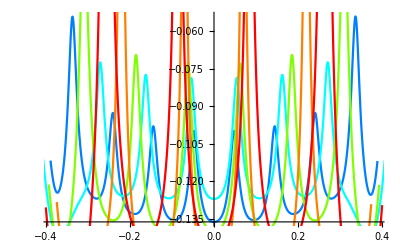

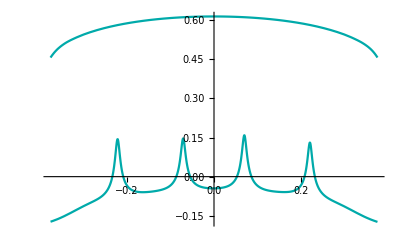

```mathematica
Show[%,%%,%%%,%%%%,%%%%%]
```

```mathematica
topcontoursG = ContourPlot[topfunction[x, y], {x, -.5, .5}, {y, -.5, .5}, ContourLabels->All]
```

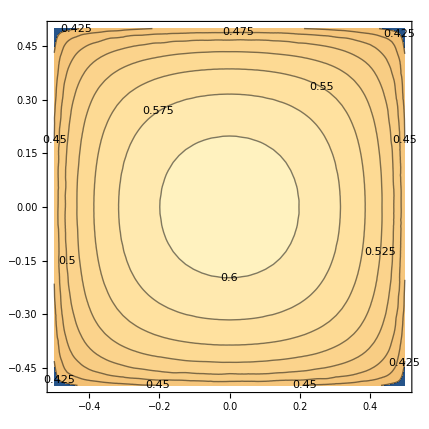

```mathematica
BoundingRegion[boxCentered]
```

Cuboid[{-0.4,-0.43301,-0.433015},{0.4,0.43301,0.433015}]

Finding E - field from the non-discrete data

```mathematica
efieldTop[u_, v_] = D[topfunction[x*.5/.43301, y*.5/.43301], {{x, y}}]/.{x->u, y->v}
efieldSideXZ[u_, v_] = D[sideFunction[z*.5/.433015, x*.5/.4], {{z, x}}]/.{x->u, z->v}
efieldSideXY[u_, v_] = D[sideFunction[y*.5/.43301, x*.5/.4], {{y, x}}]/.{x->u, y->v}
```

{1.15471 InterpolatingFunction[…][1.15471 u,1.15471 v],1.15471 InterpolatingFunction[…][1.15471 u,1.15471 v]}

{1.15469 InterpolatingFunction[…][1.15469 v,1.25 u],1.25 InterpolatingFunction[…][1.15469 v,1.25 u]}

{1.15471 InterpolatingFunction[…][1.15471 v,1.25 u],1.25 InterpolatingFunction[…][1.15471 v,1.25 u]}

```mathematica
EfieldXZ[r_] :=  {efieldSideXY[r[[1]],r[[3]]][[2]], 0, efieldSideXY[r[[1]],r[[3]]][[1]]}
EfieldXY[r_] :=  {efieldSideXZ[r[[1]],r[[2]]][[2]], efieldSideXZ[r[[1]],r[[2]]][[1]], 0}
EfieldBottom[r_] := Join[{0},efieldTop[r[[2]],r[[3]]]]
EfieldTop[r_] := Join[{0},-efieldTop[r[[2]],r[[3]]]]
```

```mathematica
EfieldKoolstra[r_]:= If[r[[1]] == .4 , EfieldBottom[r], If[ r[[1]] == -.4, EfieldTop[r], If[Abs[r[[2]]] == 0.43301, EfieldXZ[r], If[Abs[r[[3]]]==0.4330154637336504, EfieldXY[r], Null]]]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
DumpSave["KoolstraEfield.mx", "Global`"]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis

{Global`}